```mathematica
(* Problem 5*)
```

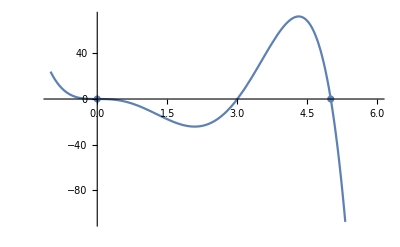

```mathematica
f[x_]:=x^3(5-x)(x-3)
Show[
Plot[f[x],{x,-1, 6}],
ListPlot[{{0,0},{5,0}},ColorFunction->Hue]
]
```

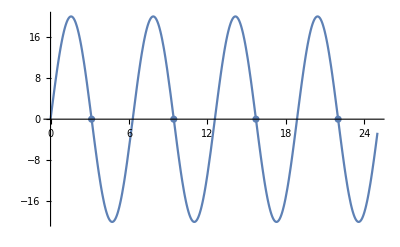

```mathematica
g[x_]:= 20Sin[x]
Show[
Plot[g[x],{x,0,25}],
ListPlot[{{Pi,0},{3Pi,0},{5Pi,0},{7Pi,0}},ColorFunction->Hue]
]
```

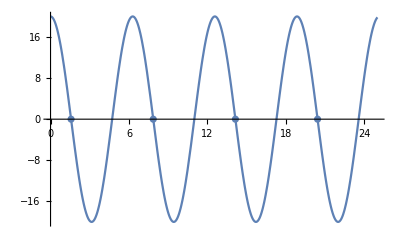

```mathematica
Show[
Plot[g'[x],{x,0,25}],
ListPlot[{{1/2 Pi,0},{1/2 Pi+2Pi,0},{1/2 Pi+4Pi,0},{1/2 Pi+6Pi,0}},ColorFunction->Hue]
]
```

```mathematica
g'[Pi]
```

-20

1/22

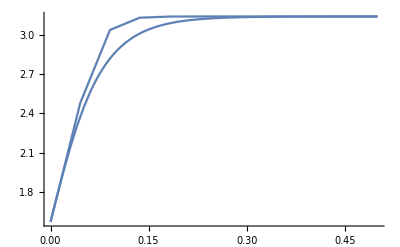

```mathematica
exactSol[t_]=u[t]/.DSolve[{u'[t]==20 Sin[u[t]],u[0]==Pi/2},u[t],t][[1]];
EulerForward[du_, du0_, t0_, T_, n_]:=Module[
{t, h, y, i, ret},

t=Subdivide[t0,T,n];
h = (T-t0)/n;
Print[h];

y= Table[0, Length[t]];

y[[1]] = du0;

For[i = 2, i≤ Length[t], i++,
y[[i]] = N[y[[i-1]]+h(du[y[[i-1]]])];
];

ret = Table[{t[[i]], y[[i]]}, {i,1,Length[t]}]
]
g[x_]:=20Sin[x]
Show[
Plot[exactSol[t],{t,0,1/2},PlotRange->All],
ListLinePlot[EulerForward[g, Pi/2, 0,1/2, 11],PlotRange->All]
]
```

```mathematica
h[t_,u_]:=20Sin[u];
RK3[du_,du0_, t_,T_, h_]:=Module[
{alphas,betas, p,n,y, i,k1,k2,k3},

n = Floor[(T-t)/h];

y= Table[0, n];
y[[1]]=du0;

For[i=2, i≤n,i++,
k1 = h*du[t+i*h, y[[i-1]]]//N;
k2 = h*du[t+i*h+1/3 h, y[[i-1]]+1/3 k1]//N;
k3=h*du[t+i*h+2/3 h, y[[i-1]]+2/3 k2]//N;
y[[i]]=y[[i-1]]+(1/4 k1+3/4 k3)//N; 
];

ret = Table[{t+(i-1)*h, y[[i]]}, {i,1,n}]
]
```

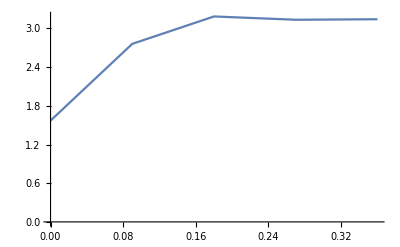

```mathematica
ListLinePlot[RK3[h, Pi/2, 0,1/2, 0.09], PlotRange->All]
```